# Thesis Chapter 03 : Plots

```mathematica
ClearAll["Global`*"]
```

## Figure 08 : Normalized array factor fora ULA with N = 8 and d = λ/2

```mathematica
nElems=8;
k=2π/λ;
d=λ/2;
u[theta_]:=k*d*Sin[theta]
AF[theta_]:=Piecewise[
{{1,Abs[Sin[u[theta]/2]]<10^-8}}
,
1/nElems*Abs[Sin[nElems*u[theta]/2]/Sin[u[theta]/2]]
]
```

```mathematica
(*3 dB level for normalized amplitude pattern*)
level3dB=1/Sqrt[2];
(*Half-power beamwidth points around the main lobe*)
thetaHP=Sort@N@{theta/. FindRoot[AF[theta]==level3dB,{theta,-0.12}],theta/. FindRoot[AF[theta]==level3dB,{theta,0.12}]};
(*First nulls around the main lobe*)
thetaNull=Sort@N@{theta/. FindRoot[AF[theta]==0,{theta,-0.26}],theta/. FindRoot[AF[theta]==0,{theta,0.26}]};
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
yFNBW=0.08;
```

```mathematica
xticks={{-Pi/2,TraditionalForm[-Pi/2]},{-Pi/4,TraditionalForm[-Pi/4]},{0,"0"},{Pi/4,TraditionalForm[Pi/4]},{Pi/2,TraditionalForm[Pi/2]}};
```

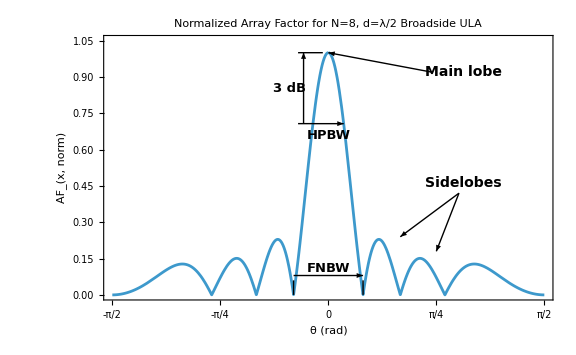

```mathematica
Plot[AF[theta],{theta,-π/2,π/2},Axes->False,Frame->True,FrameLabel->{Style["θ (rad)",FontFamily->"Times New Roman",FontSize->16],Style["AF_(x,   norm)",FontFamily->"Times New Roman",FontSize->16]},PlotLabel->Style["Normalized Array Factor for N=8, d=λ/2 Broadside ULA",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],FrameTicks->{{Automatic,None},{xticks,None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontSize->16],PlotRange->{{-π/2,+π/2},{0,1.05}},  GridLines->Automatic,GridLinesStyle->Directive[Dashed],ImageSize->Large,ImagePadding->{{50,20},{50,20}},
Epilog->{Arrowheads[0.03],Thick,
(*Main lobe annotation*)Arrow[{{0.75,0.92},{0,1}}],Text[Style["Main lobe",FontFamily->"Times New Roman",FontSize->14,Bold],{0.98,0.92}],
(*Sidelobe annotation*)Arrow[{{0.95,0.42},{π/6,0.24}}],Arrow[{{0.95,0.42},{π/4,0.18}}],Text[Style["Sidelobes",FontFamily->"Times New Roman",FontSize->14,Bold],{0.98,0.46}],
(*helper lines from left annotation position*)Line[{{-0.22,1.0},{-0.04,1.0}}],Line[{{-0.22,level3dB},{thetaHP[[1]],level3dB}}],
(*vertical double arrow for 3 dB drop*)Arrowheads[{{-0.025,0},{0.025,1}}],Arrow[{{-0.18,level3dB},{-0.18,1.0}}],Text[Style["3 dB",FontFamily->"Times New Roman",FontSize->13,Bold],{-0.28,(1+level3dB)/2}],
(*horizontal double arrow for beamwidth*)Arrowheads[{{-0.025,0},{0.025,1}}],Arrow[{{thetaHP[[1]],0.707},{thetaHP[[2]],0.707}}],Text[Style["HPBW",FontFamily->"Times New Roman",FontSize->13,Bold],{0,0.66}],
(*--------null markers--------*)Line[{{thetaNull[[1]],0},{thetaNull[[1]],0.06}}],Line[{{thetaNull[[2]],0},{thetaNull[[2]],0.06}}],Text[Style[Subscript["θ","null,L"],FontFamily->"Times New Roman",FontSize->12],{thetaNull[[1]],-0.04}],Arrowheads[{{-0.022,0},{0.022,1}}],Arrow[{{thetaNull[[1]],yFNBW},{thetaNull[[2]],yFNBW}}],
(*label*)Text[Style["FNBW",FontFamily->"Times New Roman",FontSize->13,Bold,Background->White],{0,yFNBW+0.03}]
}]
```

## Figure 08 : Normalized array factor fora ULA with N = 8 and d = λ/2

```mathematica
ClearAll["Global`*"]
λ=1;
k=2 Pi/λ;
d=λ/2;

u[theta_]:=k*d*Sin[theta];
AF[n_,theta_]:=Piecewise[{{1,Abs[Sin[u[theta]/2]]<10^-8}},(1/n)*Abs[Sin[n*u[theta]/2]/Sin[u[theta]/2]]];
AFdB[n_,theta_]:=Max[20 Log10[AF[n,theta]],-60];
```

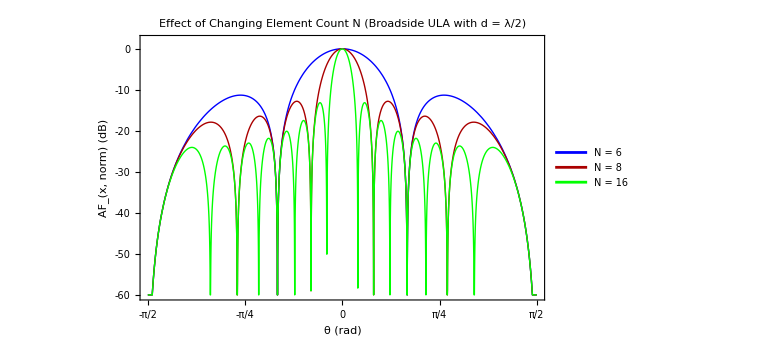

```mathematica
Plot[Evaluate@Table[AFdB[n,θ ],{n,{4,8,16}}],{θ,-π/2,π/2},Axes->False,Frame->True,FrameLabel->{Style["θ (rad)",FontFamily->"Times New Roman",FontSize->16],Style["AF_(x,   norm) (dB)",FontFamily->"Times New Roman",FontSize->16]},PlotLabel->Style["Effect of Changing Element Count N (Broadside ULA with d = λ/2)",FontFamily->"Times New Roman",FontSize->16,Bold,FontColor->Black],PlotStyle->{Directive[Blue,Thick],Directive[Darker[Red],Thick],Directive[Green,Thick]},PlotRange->{-60,2},GridLines->{Range[-π/2,π/2,π/4],Range[-60,0,10]},GridLinesStyle->Directive[Gray,Dashed,Opacity[0.5]],FrameTicks->{{Range[-60,0,10],None},{Range[-π/2,π/2,π/4],None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontSize->16],PlotLegends->Placed[LineLegend[{Style["N = 6",FontFamily->"Times New Roman",FontSize->13],Style["N = 8",FontFamily->"Times New Roman",FontSize->13],Style["N = 16",FontFamily->"Times New Roman",FontSize->13]}],{0.9,0.85}],ImageSize->Large,ImagePadding->{{70,20},{50,20}}]
```

## Figure 08 : Normalized array factor for a ULA with N = 8 and d = 1.5λ

```mathematica
ClearAll["Global`*"]
nElems=8;
k=2π/λ;
d=1.5λ;
u[theta_]:=k*d*Sin[theta]
AF[theta_]:=Piecewise[
{{1,Abs[Sin[u[theta]/2]]<10^-8}}
,
1/nElems*Abs[Sin[nElems*u[theta]/2]/Sin[u[theta]/2]]
]
```

```mathematica
xticks={{-Pi/2,TraditionalForm[-Pi/2]},{-Pi/4,TraditionalForm[-Pi/4]},{0,"0"},{Pi/4,TraditionalForm[Pi/4]},{Pi/2,TraditionalForm[Pi/2]}};
```

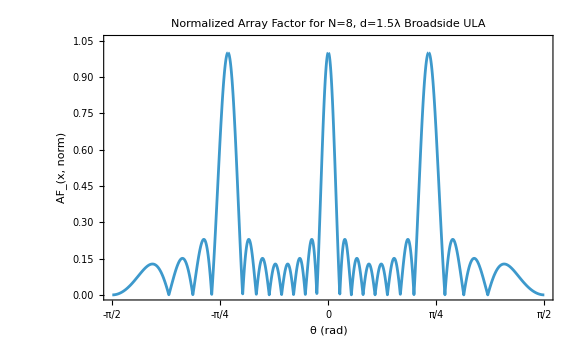

```mathematica
Plot[AF[theta],{theta,-π/2,π/2},Axes->False,Frame->True,FrameLabel->{Style["θ (rad)",FontFamily->"Times New Roman",FontSize->16],Style["AF_(x,   norm)",FontFamily->"Times New Roman",FontSize->16]},PlotLabel->Style["Normalized Array Factor for N=8, d=1.5λ Broadside ULA",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],FrameTicks->{{Automatic,None},{xticks,None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontSize->16],PlotRange->{{-π/2,+π/2},{0,1.05}},  GridLines->Automatic,GridLinesStyle->Directive[Dashed],ImageSize->Large,ImagePadding->{{50,20},{50,20}}]
```

## Figure 3.13: far-field beam steering vs near-field beam focusing

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Defien array diemntional and functional functional parameters*)
λ=1
nElems=33;
d=0.5λ;
yPositions=Table[(n-(nElems+1)/2)*d,{n,1,nElems}];
sVec[n_]:={0,yPositions[[n]]};
k=2π/λ;

(*Near field focal point*)
rf={20λ,10λ};
(*far-field direc;tional reference point on the same radial line*)
rs={80λ,40λ};
(*unit steering direction*)
rhat=rs/Norm[rs];
```

1

```mathematica
(*UPW array response*)
aUPW[r_]:=Module[{rhat=r/Norm[r]},
Table[Exp[-I*k*(rhat.sVec[n])],{n,1,nElems}]
];
```

```mathematica
(*NUSW array response*)
aNUSW[rList_]:=Module[{rr=Norm[rList]},
Table[(rr/Norm[rList-sVec[n]])*Exp[-ⅈ*k*(Norm[rList-sVec[n]]-rr)],{n,1,nElems}]
];
```

```mathematica
(*Far field steering excitation using UPW*)
wFF=aUPW[rs];
(*Near-field focusing excitation using NUSW*)
wNF=aNUSW[rf];
```

```mathematica
(*far-field Normalized Beam focusing pattern*)
psiFF[x_,y_]:=Module[{r={x,y},a},
a=aUPW[r];
Abs[Conjugate[wFF].a]/(Norm[wFF]*Norm[a])
];
(*Near-field Normalized Beam focusing pattern*)
psiNF[x_,y_]:=Module[{r={x,y},a},
a=aNUSW[r];
Abs[Conjugate[wNF].a]/(Norm[wNF]* Norm[a])];
```

```mathematica
(*Plots*)
xMin=0;xMax=40;
yMin=0;yMax=40;
farFieldPlot=DensityPlot[psiFF[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotPoints->100,MaxRecursion->5,Exclusions->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotLabel->Style["Far-field Steering Pattern (UPW)",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],FrameLabel->{Style["x/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],Style["y/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold]},LabelStyle->Directive[FontFamily->"Times",FontSize->16,Black],PlotRange->All,PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,1}},LegendMarkerSize->{15,300}],Right],ImageSize->300]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap3Fig13a.pdf"}],Rasterize[farFieldPlot,"Image",ImageResolution->300]]
```

G:\My Drive\3rd year materials\3rd year part ii\Thesis work\Thesis Mathematica codes\Thesis Chapter 3 mathemtica code\Chap3Fig13a.pdf

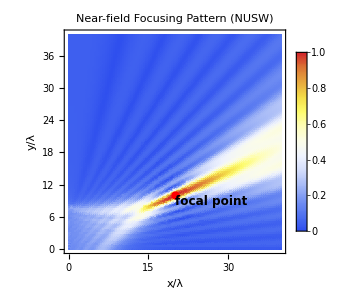

```mathematica
nearFieldPlot=DensityPlot[psiNF[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotPoints->100,MaxRecursion->5,Exclusions->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotLabel->Style["Near-field Focusing Pattern (NUSW)",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],FrameLabel->{Style["x/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],Style["y/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold]},LabelStyle->Directive[FontFamily->"Times",FontSize->16,Black],PlotRange->All,PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,1}},LegendMarkerSize->{15,300}],Right],ImageSize->300,Epilog->{Red,PointSize[0.02],Point[{20,10}],Black,Text[Style["focal point",FontFamily->"Times New Roman",FontSize->12,Bold],{20,10},{-1.2,1.2}]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap3Fig13b.pdf"}],Rasterize[nearFieldPlot,"Image",ImageResolution->300]]
```

G:\My Drive\3rd year materials\3rd year part ii\Thesis work\Thesis Mathematica codes\Thesis Chapter 3 mathemtica code\Chap3Fig13b.pdf

## Figure 3.13: far-field beam steering vs near-field beam focusing

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Defien array diemntional and functional functional parameters*)
λ=1
d=0.5λ;

(*Near field focal point*)
rf={20λ,10λ};
(*far-field direc;tional reference point on the same radial line*)
rs={80λ,40λ};
(*unit steering direction*)
rhat=rs/Norm[rs];
```

1

```mathematica
(*NUSW array response*)
aNUSW[rList_,nElems_]:=Module[{rr=Norm[rList]},
Table[(rr/Norm[rList-sVec[n]])*Exp[-ⅈ*k*(Norm[rList-sVec[n]]-rr)],{n,1,nElems}]
];
```

```mathematica
(*Near-field Normalized Beam focusing pattern*)
psiNF[x_,y_,nElems_]:=Module[{r={x,y},a},
a=aNUSW[r,nElems];
Abs[Conjugate[wNF].a]/(Norm[wNF]* Norm[a])];
```

```mathematica
(*When N=33*)
nElems1=33;
yPositions=Table[(n-(nElems1+1)/2)*d,{n,1,nElems1}];
sVec[n_]:={0,yPositions[[n]]};
k=2π/λ;
(*Near-field focusing excitation using NUSW*)
wNF=aNUSW[rf,nElems1];
```

```mathematica
xMin=0;xMax=40;
yMin=0;yMax=40;
```

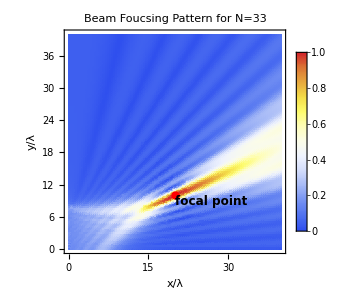

```mathematica
nearFieldPlot1=DensityPlot[psiNF[x,y,nElems1],{x,xMin,xMax},{y,yMin,yMax},PlotPoints->100,MaxRecursion->5,Exclusions->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotLabel->Style["Beam Foucsing Pattern for N=33",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],FrameLabel->{Style["x/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],Style["y/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold]},LabelStyle->Directive[FontFamily->"Times",FontSize->16,Black],PlotRange->All,PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,1}},LegendMarkerSize->{15,300}],Right],ImageSize->300,Epilog->{Red,PointSize[0.02],Point[{20,10}],Black,Text[Style["focal point",FontFamily->"Times New Roman",FontSize->12,Bold],{20,10},{-1.2,1.2}]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap3Fig14a.pdf"}],Rasterize[nearFieldPlot1,"Image",ImageResolution->300]]
```

G:\My Drive\3rd year materials\3rd year part ii\Thesis work\Thesis Mathematica codes\Thesis Chapter 3 mathemtica code\Chap3Fig14a.pdf

```mathematica
(*When N=55*)
nElems2=55;
yPositions=Table[(n-(nElems2+1)/2)*d,{n,1,nElems2}];
sVec[n_]:={0,yPositions[[n]]};
k=2π/λ;
(*Near-field focusing excitation using NUSW*)
wNF=aNUSW[rf,nElems2];
```

```mathematica
xMin=0;xMax=40;
yMin=0;yMax=40;
```

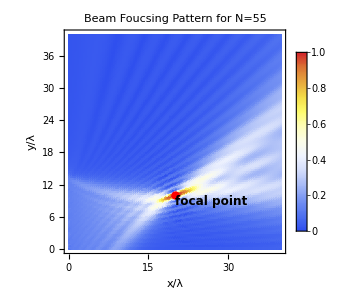

```mathematica
nearFieldPlot2=DensityPlot[psiNF[x,y,nElems2],{x,xMin,xMax},{y,yMin,yMax},PlotPoints->100,MaxRecursion->5,Exclusions->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotLabel->Style["Beam Foucsing Pattern for N=55",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],FrameLabel->{Style["x/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],Style["y/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold]},LabelStyle->Directive[FontFamily->"Times",FontSize->16,Black],PlotRange->All,PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,1}},LegendMarkerSize->{15,300}],Right],ImageSize->300,Epilog->{Red,PointSize[0.02],Point[{20,10}],Black,Text[Style["focal point",FontFamily->"Times New Roman",FontSize->12,Bold],{20,10},{-1.2,1.2}]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap3Fig14b.pdf"}],Rasterize[nearFieldPlot2,"Image",ImageResolution->300]]
```

G:\My Drive\3rd year materials\3rd year part ii\Thesis work\Thesis Mathematica codes\Thesis Chapter 3 mathemtica code\Chap3Fig14b.pdf

```mathematica
(*When N=33*)
nElems3=77;
yPositions=Table[(n-(nElems3+1)/2)*d,{n,1,nElems3}];
sVec[n_]:={0,yPositions[[n]]};
k=2π/λ;
(*Near-field focusing excitation using NUSW*)
wNF=aNUSW[rf,nElems3];
```

```mathematica
xMin=0;xMax=40;
yMin=0;yMax=40;
```

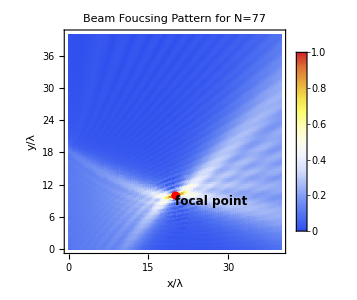

```mathematica
nearFieldPlot3=DensityPlot[psiNF[x,y,nElems3],{x,xMin,xMax},{y,yMin,yMax},PlotPoints->100,MaxRecursion->5,Exclusions->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotLabel->Style["Beam Foucsing Pattern for N=77",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],FrameLabel->{Style["x/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold],Style["y/λ",FontFamily->"Times New Roman",FontSize->16,FontColor->Black,Bold]},LabelStyle->Directive[FontFamily->"Times",FontSize->16,Black],PlotRange->All,PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,1}},LegendMarkerSize->{15,300}],Right],ImageSize->300,Epilog->{Red,PointSize[0.02],Point[{20,10}],Black,Text[Style["focal point",FontFamily->"Times New Roman",FontSize->12,Bold],{20,10},{-1.2,1.2}]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap3Fig14c.pdf"}],Rasterize[nearFieldPlot3,"Image",ImageResolution->300]]
```

G:\My Drive\3rd year materials\3rd year part ii\Thesis work\Thesis Mathematica codes\Thesis Chapter 3 mathemtica code\Chap3Fig14c.pdf

### Fig 3.15: Degree of focus

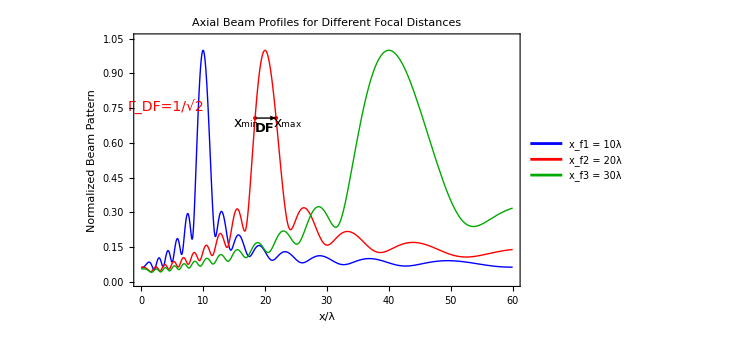

```mathematica
ClearAll["Global`*"];
λ=1;
k=2 Pi/λ;
d=λ/2;
nElems=33;
yF=10 λ;

xFList={10 λ,20 λ,40 λ};

yPositions=Table[(n-(nElems+1)/2) d,{n,1,nElems}];
sVec[n_]:={0,yPositions[[n]]};

aNUSW[r_]:=Module[{rr},rr=Norm[N[r]];
N@Table[(rr/Norm[N[r]-sVec[n]])*Exp[-I*k*(Norm[N[r]-sVec[n]]-rr)],{n,1,nElems}]];

wNF[rf_]:=aNUSW[rf];

psiNF[rf_,x_,y_]:=Module[{r,a,w},r={x,y};
a=aNUSW[r];
w=wNF[rf];
N[Abs[Conjugate[w].a]/(Norm[w] Norm[a])]];

gammaDF=1/Sqrt[2];

axialProfile[x_]:=psiNF[{20 λ,yF},x,yF];
data=Table[{x,axialProfile[x]},{x,0,40,0.01}];
aboveThreshold=Select[data,#[[2]]>=gammaDF&];
xMinDF=Min[aboveThreshold[[All,1]]];
xMaxDF=Max[aboveThreshold[[All,1]]];
DF=xMaxDF-xMinDF;

multiDoFPlot=Plot[Evaluate@Table[psiNF[{xF,yF},x,yF],{xF,xFList}],{x,0,60},PlotRange->{0,1.05},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick],Directive[Darker[Green],Thick]},Frame->True,FrameLabel->{Style["x/λ",FontFamily->"Times",FontSize->16],Style["Normalized Beam Pattern",FontFamily->"Times",FontSize->16]},PlotLabel->Style["Axial Beam Profiles for Different Focal Distances",FontFamily->"Times",FontSize->16,Bold],FrameTicksStyle->Directive[FontFamily->"Times",FontSize->13],GridLines->{{xMinDF,20 λ,xMaxDF},{gammaDF}},GridLinesStyle->Directive[Black,Dashed],PlotLegends->Placed[LineLegend[{Style["x_f1 = 10λ",FontFamily->"Times",FontSize->13],Style["x_f2 = 20λ",FontFamily->"Times",FontSize->13],Style["x_f3 = 30λ",FontFamily->"Times",FontSize->13]}],{0.9,0.85}],Epilog->{Red,PointSize[Large],Point[{xMinDF,gammaDF}],Red,PointSize[Large],Point[{xMaxDF,gammaDF}],Black,Text[Style["x_min",FontFamily->"Times",FontSize->14],{xMinDF-1.5,gammaDF-0.02}],Text[Style["x_max",FontFamily->"Times",FontSize->14],{xMaxDF+2,gammaDF-0.02}],Text[Style["\!\(\*SubscriptBox[\(Γ\), \(DF\)]\)=1/\!\(\*SqrtBox[\(2\)]\)",FontFamily->"Times",FontSize->14,Red],{4,gammaDF+0.05}],Arrowheads[{{-0.02,0},{0.02,1}}],Arrow[{{xMinDF,gammaDF},{xMaxDF,gammaDF}}],Text[Style["DF",FontFamily->"Times New Roman",FontSize->13,Bold],{20,0.66}]},ImageSize->550];

multiDoFPlot
```

### Fig 3.17 : Comparison of normalized beam pattern for collocated, Modular and Sparse antenna arrays

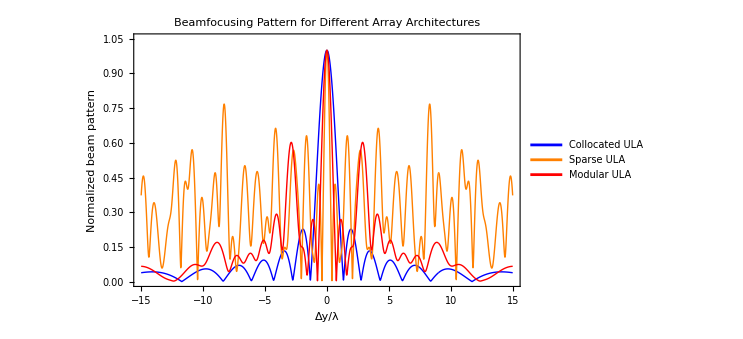

```mathematica
ClearAll["Global`*"];

(*Parameters*)
lambda=1.0;
k=2 Pi/lambda;

(*Focal point*)
xF=10 lambda;
yF=0 lambda;
rF=Sqrt[xF^2+yF^2];

(*Transverse cut through focal point:x=xF,vary y*)
yMin=-15 lambda;
yMax=15 lambda;

(*ULA element coordinates along y-axis*)

(*1) Collocated ULA*)
Ncol=16;
dcol=lambda/2;
yCol=Table[(n-(Ncol+1)/2) dcol,{n,1,Ncol}];

(*2) Sparse ULA*)
Nsp=16;
dsp=8 lambda;
ySparse=Table[(n-(Nsp+1)/2) dsp,{n,1,Nsp}];

(*3) Modular ULA:Q modules,M elements per module*)
Q=4;
M=4;
dmod=lambda/2;
Dmod=4 lambda;

moduleCenters=Table[(q-(Q+1)/2) Dmod,{q,1,Q}];
localCoords=Table[(m-(M+1)/2) dmod,{m,1,M}];

yMod=Flatten@Table[moduleCenters[[q]]+localCoords[[m]],{q,1,Q},{m,1,M}];

(*Full NUSW response with amplitude variation*)
aNUSW[yCoords_,x_,y_]:=Module[{R},R=Sqrt[x^2+(y-#)^2]&/@yCoords;
(rF/R) Exp[-I k R]];

(*Beamfocusing field*)
psiField[yCoords_,xObs_,yObs_,xFoc_,yFoc_]:=Module[{aObs,aFoc},aObs=aNUSW[yCoords,xObs,yObs];
aFoc=aNUSW[yCoords,xFoc,yFoc];
Conjugate[aFoc].aObs];

(*Magnitude along the transverse cut x=xF*)
psiCol[y_]:=Abs[psiField[yCol,xF,y,xF,yF]];
psiSparse[y_]:=Abs[psiField[ySparse,xF,y,xF,yF]];
psiMod[y_]:=Abs[psiField[yMod,xF,y,xF,yF]];

(*Dense sampling+max normalization*)
ySamples=Subdivide[yMin,yMax,10000];

colVals=psiCol/@ySamples;
sparseVals=psiSparse/@ySamples;
modVals=psiMod/@ySamples;

colValsN=colVals/Max[colVals];
sparseValsN=sparseVals/Max[sparseVals];
modValsN=modVals/Max[modVals];

(*Linear plot*)
plotLinear=ListLinePlot[{Transpose[{ySamples/lambda,colValsN}],Transpose[{ySamples/lambda,sparseValsN}],Transpose[{ySamples/lambda,modValsN}]},PlotStyle->{Directive[Blue,Thick],Directive[Orange,Thick],Directive[Red,Thick]},PlotLegends->Placed[LineLegend[{"Collocated ULA","Sparse ULA","Modular ULA"},LabelStyle->Directive[FontFamily->"Times New Roman",14]],{0.18,0.85}],PlotRange->{{yMin/lambda,yMax/lambda},{0,1.05}},Frame->True,Axes->False,FrameLabel->{Style["Δy/λ",14,FontFamily->"Times New Roman"],Style["Normalized beam pattern",14,FontFamily->"Times New Roman"]},FrameTicksStyle->Directive[FontFamily->"Times New Roman",14],LabelStyle->Directive[FontFamily->"Times New Roman",14],BaseStyle->{FontFamily->"Times New Roman"},ImageSize->550,PlotLabel->Style["Beamfocusing Pattern for Different Array Architectures",15,Bold],LabelStyle->Directive[14],ImageSize->Large];

plotLinear
```

```mathematica
(*Full NUSW response with amplitude variation*)aNUSW[yCoords_,x_,y_]:=Module[{R,r0},R=Sqrt[x^2+(y-#)^2]&/@yCoords;
r0=Sqrt[x^2+y^2];
(r0/R) Exp[-I k R]];

(*2D plotting region in normalized coordinates*)
Xmin=3;
Xmax=20;
Ymin=-15;
Ymax=15;

(*2D fields*)
psiCol2D[x_,y_]:=Abs[psiField[yCol,x,y,xF,yF]];
psiSparse2D[x_,y_]:=Abs[psiField[ySparse,x,y,xF,yF]];
psiMod2D[x_,y_]:=Abs[psiField[yMod,x,y,xF,yF]];

(*Normalize by value at the intended focal point*)
normCol=psiCol2D[xF,yF];
normSparse=psiSparse2D[xF,yF];
normMod=psiMod2D[xF,yF];

pCol=DensityPlot[Min[psiCol2D[X lambda,Y lambda]/normCol,1],{X,Xmin,Xmax},{Y,Ymin,Ymax},PlotRange->All,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotPoints->150,MaxRecursion->2,FrameLabel->{Style["x/λ",14,Bold,FontFamily->"Times New Roman"],Style["y/λ",16,Bold,FontFamily->"Times New Roman"]},PlotLabel->Style["Beam focusing pattern for Collocated ULA",16,Bold,FontFamily->"Times New Roman"],LabelStyle->Directive[FontFamily->"Times",FontSize->16,Black],Epilog->{Black,PointSize[0.015],Point[{xF/lambda,yF/lambda}]},ImageSize->Medium]
```

-Graphics-

```mathematica
pSparse=DensityPlot[Min[psiSparse2D[X lambda,Y lambda]/normSparse,1],{X,Xmin,Xmax},{Y,Ymin,Ymax},PlotRange->All,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotPoints->150,MaxRecursion->2,FrameLabel->{Style["x/λ",14,Bold,FontFamily->"Times New Roman"],Style["y/λ",16,Bold,FontFamily->"Times New Roman"]},PlotLabel->Style["Beam focusing pattern for Sparse ULA",16,Bold,FontFamily->"Times New Roman"],LabelStyle->Directive[FontFamily->"Times",FontSize->16,Black],Epilog->{Black,PointSize[0.018],Point[{xF/lambda,yF/lambda}]},ImageSize->Medium]
```

-Graphics-

```mathematica
pMod=DensityPlot[Min[psiMod2D[X lambda,Y lambda]/normMod,1],{X,Xmin,Xmax},{Y,Ymin,Ymax},PlotRange->{0,1},ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotPoints->150,MaxRecursion->2,FrameLabel->{Style["x/λ",14,Bold,FontFamily->"Times New Roman"],Style["y/λ",16,Bold,FontFamily->"Times New Roman"]},PlotLabel->Style["Beam focusing pattern for Modular ULA",16,Bold,FontFamily->"Times New Roman"],LabelStyle->Directive[FontFamily->"Times",FontSize->16,Black],Epilog->{Black,PointSize[0.018],Point[{xF/lambda,yF/lambda}]},PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,1}},LegendMarkerSize->{15,300}],Right],ImageSize->360]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Chap3Fig16c.pdf"}],Rasterize[pMod,"Image",ImageSize->360,ImageResolution->300]]
```

G:\My Drive\3rd year materials\3rd year part ii\Thesis work\Thesis Mathematica codes\Thesis Chapter 3 mathemtica code\Chap3Fig16c.pdf

```mathematica
ClearAll["Global`*"];

(*Parameters*)
NM=16;        (*total elements*)
Nmod=4;       (*number of modules*)
Mmod=4;       (*elements per module*)

dbar=1/2;     (*collocated spacing d/lambda*)
Isp=4;        (*sparse spacing factor:d_s=Isp lambda/2*)
gamma=13;     (*modular separation parameter*)

(*Stable Dirichlet kernel*)
Xi[M_,d_,u_]:=If[Abs[Sin[Pi d u]]<10^-10,1,Abs[Sin[Pi M d u]/(M Sin[Pi d u])]];

(*Spatial-frequency difference u=Delta_theta*)
Gcol[u_]:=Xi[NM,1/2,u];

Gsp[u_]:=Xi[NM,Isp/2,u];

Gmod[u_]:=Xi[Nmod,gamma/2,u] Xi[Mmod,1/2,u];

(*Smooth sampled plot*)
uMin=-1;
uMax=1;
uSamples=Subdivide[uMin,uMax,5000];

colData=Transpose[{uSamples,Gcol/@uSamples}];
spData=Transpose[{uSamples,Gsp/@uSamples}];
modData=Transpose[{uSamples,Gmod/@uSamples}];

ListLinePlot[{colData,spData,modData},PlotStyle->{Directive[Blue,Thick],Directive[Orange,Thick],Directive[Red,Thick]},PlotLegends->Placed[{"collocated ULA","sparse ULA","modular ULA"},{0.18,0.82}],PlotRange->{{uMin,uMax},{0,1.05}},AxesLabel->{Style["Δθ",14,Bold],Style["Normalized beam pattern",14,Bold]},LabelStyle->Directive[14],ImageSize->Large]
```

-Graphics-

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*Normalized parameters*)
(* =====================================================*)

lambda=1;
k=2 Pi/lambda;
h=30 lambda;      (*distance from array plane to receiver plane*)

xF=0;             (*focal point on receiver plane*)
yF=0;

xMin=-12 lambda;
xMax=12 lambda;

(*Helper:planar grid coordinates*)
planarCoords[Nx_,Ny_,dx_,dy_]:=Flatten[Table[{(ix-(Nx+1)/2) dx,(iy-(Ny+1)/2) dy},{ix,1,Nx},{iy,1,Ny}],1];

(*1. Collocated planar array*)

NxCol=9;
NyCol=9;
dCol=lambda/2;

coordsCol=planarCoords[NxCol,NyCol,dCol,dCol];

(*2. Sparse planar array*)

NxSp=9;
NySp=9;
dSp=6 lambda;

coordsSparse=planarCoords[NxSp,NySp,dSp,dSp];

(*3. Modular planar array*)

Qx=3;Qy=3;      (*number of modules*)
Mx=3;My=3;      (*elements per module*)

dMod=lambda/2;     (*intra-module spacing*)
Dmod=3 lambda;     (*inter-module centre spacing*)

moduleCenters=planarCoords[Qx,Qy,Dmod,Dmod];
localCoords=planarCoords[Mx,My,dMod,dMod];

coordsMod=Flatten[Table[moduleCenters[[q]]+localCoords[[m]],{q,1,Length[moduleCenters]},{m,1,Length[localCoords]}],1];

(* =====================================================*)
(*NUSW array response*)
(*Array plane:z=h*)
(*Receiver plane:z=0*)
(*Observation point:(x,y,0)*)
(*Element location:(xe,ye,h)*)
(* =====================================================*)

aNUSW[coords_,x_,y_]:=Module[{r},r=Sqrt[(x-#[[1]])^2+(y-#[[2]])^2+h^2]&/@coords;
Exp[-I k r]/r];

(*To include amplitude variation,use this version instead:aNUSW[coords_,x_,y_]:=Module[{r},r=Sqrt[(x-#[[1]])^2+(y-#[[2]])^2+h^2]&/@coords;
Exp[-I k r]/r];*)

(*Beamfocusing field using conjugate phase*)

psiField[coords_,x_,y_,xFoc_,yFoc_]:=Module[{aObs,aFoc},aObs=aNUSW[coords,x,y];
aFoc=aNUSW[coords,xFoc,yFoc];
Conjugate[aFoc].aObs];

(*x-axis cut on receiver plane:y=0*)
psiCol[x_]:=Abs[psiField[coordsCol,x,0,xF,yF]];
psiSparse[x_]:=Abs[psiField[coordsSparse,x,0,xF,yF]];
psiMod[x_]:=Abs[psiField[coordsMod,x,0,xF,yF]];

(*Dense sampling and normalization*)

xSamples=Subdivide[xMin,xMax,5000];

colVals=psiCol/@xSamples;
sparseVals=psiSparse/@xSamples;
modVals=psiMod/@xSamples;

colValsN=colVals/Max[colVals];
sparseValsN=sparseVals/Max[sparseVals];
modValsN=modVals/Max[modVals];

(*Plot in normalized coordinate x/lambda*)

plotLinear=ListLinePlot[{Transpose[{xSamples/lambda,colValsN}],Transpose[{xSamples/lambda,sparseValsN}],Transpose[{xSamples/lambda,modValsN}]},PlotStyle->{Directive[Blue,Thick],Directive[Orange,Thick],Directive[Red,Thick]},PlotLegends->Placed[{"collocated XL-array","sparse XL-array","modular XL-array"},{0.18,0.82}],PlotRange->{{xMin/lambda,xMax/lambda},{0,1.05}},AxesLabel->{Style["x/λ",14,Bold],Style["|ψ∼|",14,Bold]},LabelStyle->Directive[14],ImageSize->Large];

plotLinear
```

$Aborted

$Aborted

Transpose::nmtx: The first two levels of {{-12,-7497/625,-7494/625,-7491/625,-7488/625,-1497/125,-7482/625,-7479/625,-7476/625,-7473/625,-1494/125,-7467/625,-7464/625,-7461/625,-7458/625,-1491/125,-7452/625,-7449/625,-7446/625,-7443/625,-1488/125,-7437/625,-7434/625,-7431/625,-7428/625,-297/25,-7422/625,-7419/625,-7416/625,-7413/625,-1482/125,-7407/625,-7404/625,-7401/625,-7398/625,-1479/125,-7392/625,-7389/625,-7386/625,-7383/625,-1476/125,-7377/625,-7374/625,-7371/625,-7368/625,-1473/125,-7362/625,-7359/625,-7356/625,-7353/625,«4951»},1} cannot be transposed.

Transpose::nmtx: The first two levels of {{-12.,-11.9952,-11.9904,-11.9856,-11.9808,-11.976,-11.9712,-11.9664,-11.9616,-11.9568,-11.952,-11.9472,-11.9424,-11.9376,-11.9328,-11.928,-11.9232,-11.9184,-11.9136,-11.9088,-11.904,-11.8992,-11.8944,-11.8896,-11.8848,-11.88,-11.8752,-11.8704,-11.8656,-11.8608,-11.856,-11.8512,-11.8464,-11.8416,-11.8368,-11.832,-11.8272,-11.8224,-11.8176,-11.8128,-11.808,-11.8032,-11.7984,-11.7936,-11.7888,-11.784,-11.7792,-11.7744,-11.7696,-11.7648,«4951»},1.} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

$Aborted

plotLinear